```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
ToString/@Range[1,5]
```

{1,2,3,4,5}

```mathematica
Evaluate[Style[#,5]&/@(ToString/@Range[1,5])]
```

{1,2,3,4,5}

```mathematica
a4shortside
```

75600/127

```mathematica
datasy[i_]:=datasy[i]=Import["iteration_s"<>ToString[i]<>"_a0_1.csv"]
```

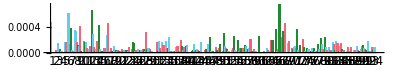

```mathematica
BarChart[T@Table[datasy[i][[;;,2]],{i,3}],AspectRatio->1/(a4longside*4/a4shortside),ImageSize->{a4longside*4,a4shortside},ChartStyle->{blue,red,green},ChartLegends->Placed[LineLegend[{blue,red,green},{"A","B","C"}],Bottom],ChartLabels->{Evaluate[Style[#,12]&/@(ToString/@Range[1,94])],None}]
```

```mathematica
Export["testchart.pdf",%]
```

testchart.pdf